# L Nl Pet Site

```mathematica
t=0.2;c=2;W=6;K=20;l = t*c;
```

```mathematica
fn[t_,W_]:=RandomReal[{W-t,W+t},K]
```

```mathematica
g = fn[t,W];
```

```mathematica
Ox = Table[0,{x,2K+1},{y,2K+1}];
```

```mathematica
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++]
i=1;While[i<K,{Ox[[i+1,i+K]] = t,Ox[[i+K,i+1]]=t};i++]
i=1;While[i<K,{Ox[[i,i+1+K]] = t ,Ox[[i+K+1,i]]=t};i++]
Ox[[2K+1,1]]=t;Ox[[1,2K+1]] = t; Ox[[2K+1,2K+1]] = W;
```

```mathematica
Ox;
```

```mathematica
ml=Ox[[1;;K,K+1;;2K]]
```

(5.88977 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.2 | 6.10373 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2 | 6.06288 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.2 | 6.05852 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.2 | 5.83735 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.2 | 6.12498 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 5.95778 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.00888 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.00183 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.03919 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.04191 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.87812 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.11857 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.17729 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.10367 | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.11537 | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.86871 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.17161 | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.87791 | 0.2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.90053)

```mathematica
Ox = Table[0,{x,2K+1},{y,2K+1}];
```

```mathematica
Ox[[2K+1,1]]=l/c;Ox[[1,2K+1]] = l/c; Ox[[2K+1,2K+1]] = W;
i=1;
While[i<K+1,{j=1;
While[j<K+1,{Ox[[i,j+K]] = l/Power[c,Abs[i-j]],Ox[[j+K,i]] = l/Power[c,Abs[i-j]]};j++]};i++]
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++](*Exponentially decaying hopping terms*)
```

```mathematica
Ox;
```

```mathematica
mnl=Ox[[1;;K,K+1;;2K]]
```

(5.88977 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563 | 0.0000488281 | 0.0000244141 | 0.000012207 | 6.10352×10^-6 | 3.05176×10^-6 | 1.52588×10^-6 | 7.62939×10^-7
0.2 | 6.10373 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563 | 0.0000488281 | 0.0000244141 | 0.000012207 | 6.10352×10^-6 | 3.05176×10^-6 | 1.52588×10^-6
0.1 | 0.2 | 6.06288 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563 | 0.0000488281 | 0.0000244141 | 0.000012207 | 6.10352×10^-6 | 3.05176×10^-6
0.05 | 0.1 | 0.2 | 6.05852 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563 | 0.0000488281 | 0.0000244141 | 0.000012207 | 6.10352×10^-6
0.025 | 0.05 | 0.1 | 0.2 | 5.83735 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563 | 0.0000488281 | 0.0000244141 | 0.000012207
0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.12498 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563 | 0.0000488281 | 0.0000244141
0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 5.95778 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563 | 0.0000488281
0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.00888 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313 | 0.0000976563
0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.00183 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625 | 0.000195313
0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.03919 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125 | 0.000390625
0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.04191 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625 | 0.00078125
0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 5.87812 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125 | 0.0015625
0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.11857 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625 | 0.003125
0.0000488281 | 0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.17729 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625
0.0000244141 | 0.0000488281 | 0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.10367 | 0.2 | 0.1 | 0.05 | 0.025 | 0.0125
0.000012207 | 0.0000244141 | 0.0000488281 | 0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.11537 | 0.2 | 0.1 | 0.05 | 0.025
6.10352×10^-6 | 0.000012207 | 0.0000244141 | 0.0000488281 | 0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 5.86871 | 0.2 | 0.1 | 0.05
3.05176×10^-6 | 6.10352×10^-6 | 0.000012207 | 0.0000244141 | 0.0000488281 | 0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 6.17161 | 0.2 | 0.1
1.52588×10^-6 | 3.05176×10^-6 | 6.10352×10^-6 | 0.000012207 | 0.0000244141 | 0.0000488281 | 0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 5.87791 | 0.2
7.62939×10^-7 | 1.52588×10^-6 | 3.05176×10^-6 | 6.10352×10^-6 | 0.000012207 | 0.0000244141 | 0.0000488281 | 0.0000976563 | 0.000195313 | 0.000390625 | 0.00078125 | 0.0015625 | 0.003125 | 0.00625 | 0.0125 | 0.025 | 0.05 | 0.1 | 0.2 | 5.90053)

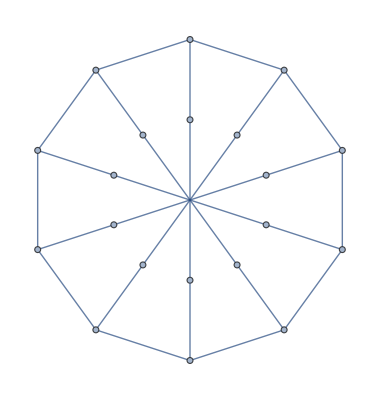

```mathematica
p =PetersenGraph[K/2,K/4,EdgeStyle->Thick]
```

```mathematica
mat = WeightedAdjacencyMatrix[p]
```

SparseArray[…]

```mathematica
Normal[mat]
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
i=1;
While[i<K+1,{mat[[i,i]]=g[[i]]};i++]
```

```mathematica
i=1;
While[i<K+1,{j=1;
While[j<K+1,{If[i==j,mat[[i,j]]=mat[[i,j]],mat[[i,j]]=l*mat[[i,j]]/Power[c,Abs[i-j]]]};j++]};i++]
```

```mathematica
mpet=Normal[mat]
```

(5.88977 | 0 | 0 | 0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.10373 | 0 | 0 | 0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6.06288 | 0 | 0 | 0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6.05852 | 0 | 0 | 0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5.83735 | 0 | 0 | 0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0
0.0125 | 0 | 0 | 0 | 0 | 6.12498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0
0 | 0.0125 | 0 | 0 | 0 | 0 | 5.95778 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0
0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 6.00888 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0
0 | 0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 6.00183 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0
0 | 0 | 0 | 0 | 0.0125 | 0 | 0 | 0 | 0 | 6.03919 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625
0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04191 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00078125
0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.87812 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.11857 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.17729 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.10367 | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.11537 | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.86871 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 6.17161 | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.87791 | 0.2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000390625 | 0.00078125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.90053)

```mathematica
Eigenvalues[ml]
Eigenvalues[mnl]
Eigenvalues[mpet]
```

{6.48528,6.41317,6.39226,6.37652,6.33576,6.28421,6.21754,6.16458,6.098,6.03188,5.98984,5.91862,5.86827,5.80808,5.73158,5.70498,5.68141,5.62705,5.61055,5.59904}

{6.80118,6.68293,6.51926,6.38909,6.25603,6.1291,6.04781,5.98993,5.9458,5.9254,5.88068,5.86002,5.84125,5.78544,5.76823,5.74145,5.71641,5.70622,5.6796,5.67276}

{6.48436,6.38282,6.29695,6.18051,6.12564,6.10479,6.06563,6.06115,6.05969,6.03996,6.00962,6.00612,5.9992,5.95672,5.8891,5.8624,5.83657,5.7058,5.66088,5.61066}

```mathematica
ec1=Eigenvectors[ml];
ec2=Eigenvectors[mnl];
ec3=Eigenvectors[mpet];
```

```mathematica
Min[Abs[ec1]]
Min[Abs[ec2]]
Min[Abs[ec3]]
```

0.000256432

2.53×10^-15

5.65072×10^-7

```mathematica
e1=Eigenvectors[ml][[-1]]
e2=Eigenvectors[mnl][[-1]]
e3=Eigenvectors[mpet][[-1]]
```

{0.0716082,-0.104093,0.191065,-0.339025,0.58781,-0.361375,0.362497,-0.288846,0.229412,-0.173185,0.151727,-0.162793,0.0754344,-0.0331615,0.0204435,-0.0184206,0.0271126,-0.0181373,0.024812,-0.0164592}

{2.53×10^-15,1.84904×10^-14,-1.31487×10^-12,5.31556×10^-11,-1.27385×10^-10,-1.34858×10^-11,3.46509×10^-10,-1.70658×10^-9,1.0033×10^-8,-1.23091×10^-7,2.03615×10^-6,-5.44866×10^-6,-0.0000121151,-0.000092963,-0.00257247,-0.0406548,0.140384,0.145172,-0.778159,0.593318}

{0.000040973,-0.0000526142,0.000046727,-0.000066979,0.000229985,-0.000184142,0.000550332,-0.000381746,0.000601268,-0.000384103,-0.0233829,0.0488018,-0.0418786,0.0575514,-0.121171,0.241139,-0.487358,0.387672,-0.599966,0.414014}

```mathematica
Min[Abs[e1]]
Min[Abs[e2]]
Min[Abs[e3]]
```

0.0164592

2.53×10^-15

0.000040973

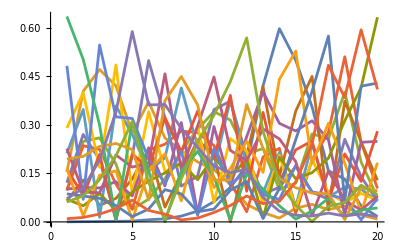

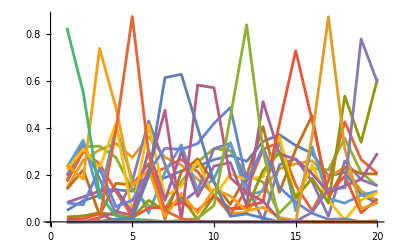

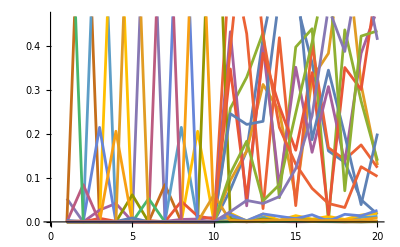

```mathematica
ListLinePlot[Abs[ec1]]
ListLinePlot[Abs[ec2]]
ListLinePlot[Abs[ec3]]
```

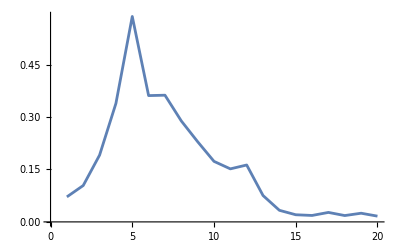

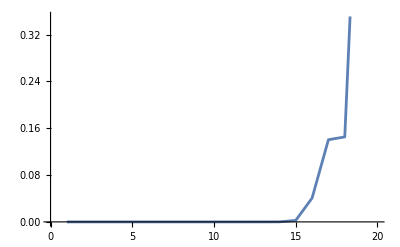

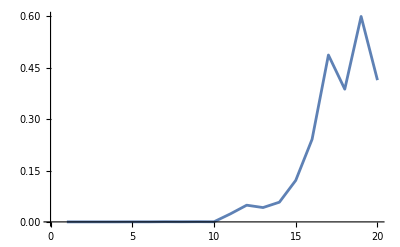

```mathematica
ListLinePlot[Abs[e1]]
ListLinePlot[Abs[e2]]
ListLinePlot[Abs[e3]]
```

```mathematica
L Nl Pet Site
```

L Nl Pet Site

```mathematica
L Nl Pet Site
```

L Nl Pet Site

```mathematica
t=0.25;c=2;W=5;K=12;l=t*c;
fn[t_,W_]:=RandomReal[{W- t/2,W+t/2},K]  ;
g = fn[t,W];
Ox = Table[0,{x,2K+1},{y,2K+1}]; 
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i+K]] = t,Ox[[i+K,i+1]]=t};i++];
i=1;While[i<K,{Ox[[i,i+1+K]] = t ,Ox[[i+K+1,i]]=t};i++];
Ox[[2K+1,1]]=t;Ox[[1,2K+1]] = t; Ox[[2K+1,2K+1]] = W;
Ox;
ml=Ox[[1;;K,K+1;;2K]];
Ox = Table[0,{x,2K+1},{y,2K+1}]; 
Ox[[2K+1,1]]=l/c;Ox[[1,2K+1]] = l/c; Ox[[2K+1,2K+1]] = W;
i=1;
While[i<K+1,{j=1;
While[j<K+1,{Ox[[i,j+K]] = l/Power[c,Abs[i-j]],Ox[[j+K,i]] = l/Power[c,Abs[i-j]]};j++]};i++];
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++](*Exponentially decaying hopping terms*);
Ox;
mnl=Ox[[1;;K,K+1;;2K]];
p =PetersenGraph[K/2,K/4,EdgeStyle->Thick];
mat = WeightedAdjacencyMatrix[p];
i=1;
While[i<K+1,{mat[[i,i]]=g[[i]]};i++];
i=1;
While[i<K+1,{j=1;
While[j<K+1,{If[i==j,mat[[i,j]]=mat[[i,j]],mat[[i,j]]=l*mat[[i,j]]/Power[c,Abs[i-j]]]};j++]};i++];
mpet=Normal[mat];
```

```mathematica
mpet
```

(4.94217 | 0 | 0 | 0.0625 | 0 | 0 | 0.0078125 | 0 | 0 | 0 | 0 | 0
0 | 5.09849 | 0 | 0 | 0.0625 | 0 | 0 | 0.0078125 | 0 | 0 | 0 | 0
0 | 0 | 4.89601 | 0 | 0 | 0.0625 | 0 | 0 | 0.0078125 | 0 | 0 | 0
0.0625 | 0 | 0 | 5.05782 | 0 | 0 | 0 | 0 | 0 | 0.0078125 | 0 | 0
0 | 0.0625 | 0 | 0 | 4.88225 | 0 | 0 | 0 | 0 | 0 | 0.0078125 | 0
0 | 0 | 0.0625 | 0 | 0 | 5.02833 | 0 | 0 | 0 | 0 | 0 | 0.0078125
0.0078125 | 0 | 0 | 0 | 0 | 0 | 4.91416 | 0.25 | 0 | 0 | 0 | 0.015625
0 | 0.0078125 | 0 | 0 | 0 | 0 | 0.25 | 4.97754 | 0.25 | 0 | 0 | 0
0 | 0 | 0.0078125 | 0 | 0 | 0 | 0 | 0.25 | 5.0871 | 0.25 | 0 | 0
0 | 0 | 0 | 0.0078125 | 0 | 0 | 0 | 0 | 0.25 | 4.98759 | 0.25 | 0
0 | 0 | 0 | 0 | 0.0078125 | 0 | 0 | 0 | 0 | 0.25 | 5.08147 | 0.25
0 | 0 | 0 | 0 | 0 | 0.0078125 | 0.015625 | 0 | 0 | 0 | 0.25 | 4.89103)

```mathematica
ml
```

(4.94217 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.25 | 5.09849 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.25 | 4.89601 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.25 | 5.05782 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.25 | 4.88225 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.25 | 5.02833 | 0.25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.25 | 4.91416 | 0.25 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 4.97754 | 0.25 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 5.0871 | 0.25 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 4.98759 | 0.25 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 5.08147 | 0.25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 4.89103)

```mathematica
mnl
```

(4.94217 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125 | 0.00390625 | 0.00195313 | 0.000976563 | 0.000488281 | 0.000244141
0.25 | 5.09849 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125 | 0.00390625 | 0.00195313 | 0.000976563 | 0.000488281
0.125 | 0.25 | 4.89601 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125 | 0.00390625 | 0.00195313 | 0.000976563
0.0625 | 0.125 | 0.25 | 5.05782 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125 | 0.00390625 | 0.00195313
0.03125 | 0.0625 | 0.125 | 0.25 | 4.88225 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125 | 0.00390625
0.015625 | 0.03125 | 0.0625 | 0.125 | 0.25 | 5.02833 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125
0.0078125 | 0.015625 | 0.03125 | 0.0625 | 0.125 | 0.25 | 4.91416 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625
0.00390625 | 0.0078125 | 0.015625 | 0.03125 | 0.0625 | 0.125 | 0.25 | 4.97754 | 0.25 | 0.125 | 0.0625 | 0.03125
0.00195313 | 0.00390625 | 0.0078125 | 0.015625 | 0.03125 | 0.0625 | 0.125 | 0.25 | 5.0871 | 0.25 | 0.125 | 0.0625
0.000976563 | 0.00195313 | 0.00390625 | 0.0078125 | 0.015625 | 0.03125 | 0.0625 | 0.125 | 0.25 | 4.98759 | 0.25 | 0.125
0.000488281 | 0.000976563 | 0.00195313 | 0.00390625 | 0.0078125 | 0.015625 | 0.03125 | 0.0625 | 0.125 | 0.25 | 5.08147 | 0.25
0.000244141 | 0.000488281 | 0.000976563 | 0.00195313 | 0.00390625 | 0.0078125 | 0.015625 | 0.03125 | 0.0625 | 0.125 | 0.25 | 4.89103)

```mathematica
ec1=Eigenvectors[ml]
ec2=Eigenvectors[mnl]
ec3=Eigenvectors[mpet]
```

(0.0458179 | 0.0999616 | 0.109768 | 0.159789 | 0.164926 | 0.239565 | 0.27517 | 0.391607 | 0.523801 | 0.447516 | 0.37124 | 0.155572
0.233925 | 0.474023 | 0.430245 | 0.477269 | 0.316099 | 0.239042 | 0.0859074 | -0.0553344 | -0.190208 | -0.219834 | -0.215319 | -0.0965135
0.252067 | 0.432771 | 0.22036 | -0.0137463 | -0.237602 | -0.451144 | -0.381477 | -0.246551 | -0.00694295 | 0.238655 | 0.373326 | 0.194292
-0.253469 | -0.352025 | -0.0153251 | 0.327911 | 0.319042 | 0.191656 | -0.118919 | -0.370137 | -0.342771 | 0.0928006 | 0.454794 | 0.285423
-0.285805 | -0.281833 | 0.184108 | 0.497379 | 0.0762647 | -0.403893 | -0.335343 | 0.03564 | 0.365445 | 0.112868 | -0.274654 | -0.23067
-0.226001 | -0.0674683 | 0.248045 | 0.187319 | -0.278781 | -0.337367 | 0.29434 | 0.458213 | -0.222376 | -0.395682 | 0.176147 | 0.35012
-0.557106 | 0.136713 | 0.438074 | -0.163326 | -0.322438 | 0.165165 | 0.224982 | -0.195169 | -0.149476 | 0.318505 | 0.0134435 | -0.329295
-0.404692 | 0.213451 | 0.158646 | -0.267833 | 0.106523 | 0.237182 | -0.313367 | -0.107008 | 0.384947 | -0.319193 | -0.158595 | 0.49121
-0.346109 | 0.342453 | -0.20685 | -0.175983 | 0.462386 | -0.170687 | -0.234675 | 0.376591 | -0.191218 | -0.0765386 | 0.280855 | -0.357839
-0.216343 | 0.283285 | -0.331726 | 0.0898329 | 0.172539 | -0.274403 | 0.281345 | -0.0624772 | -0.190697 | 0.422733 | -0.439651 | 0.397927
-0.18356 | 0.284675 | -0.435925 | 0.310887 | -0.190034 | -0.0617224 | 0.307029 | -0.380036 | 0.336117 | -0.336089 | 0.246173 | -0.182855
0.0905699 | -0.165222 | 0.314143 | -0.349847 | 0.485908 | -0.4201 | 0.425246 | -0.308011 | 0.180221 | -0.125235 | 0.0709935 | -0.043832)

(-0.138432 | -0.229235 | -0.243584 | -0.322686 | -0.307451 | -0.364838 | -0.338362 | -0.350599 | -0.362367 | -0.290899 | -0.250098 | -0.145961
0.258547 | 0.405524 | 0.346155 | 0.362072 | 0.212849 | 0.104328 | -0.0478808 | -0.194392 | -0.339722 | -0.351419 | -0.36496 | -0.222289
-0.314705 | -0.437669 | -0.197863 | 0.00966473 | 0.206808 | 0.406733 | 0.335902 | 0.220761 | -0.00778657 | -0.233522 | -0.412325 | -0.275303
-0.294841 | -0.335926 | 0.0296719 | 0.366541 | 0.285667 | 0.176253 | -0.121731 | -0.35189 | -0.395027 | 0.00734536 | 0.401946 | 0.30986
-0.277116 | -0.219732 | 0.193838 | 0.515994 | 0.0404215 | -0.415718 | -0.294669 | -0.00396332 | 0.426169 | 0.170024 | -0.225739 | -0.219806
0.190192 | -0.00530973 | -0.166518 | -0.187414 | 0.208578 | 0.408732 | -0.261426 | -0.541211 | 0.242328 | 0.422557 | -0.115857 | -0.280047
0.771619 | -0.496166 | -0.221341 | 0.215873 | 0.0806647 | -0.118918 | -0.0333203 | 0.0833447 | 0.049911 | -0.14197 | -0.00241834 | 0.107114
-0.0998393 | 0.100086 | -0.0243172 | -0.0939537 | 0.0971646 | 0.150795 | -0.202727 | -0.179084 | 0.521132 | -0.539789 | -0.142762 | 0.530957
0.00928235 | -0.0207972 | 0.0256101 | 0.0174181 | -0.045803 | -0.02726 | 0.0809266 | 0.00976428 | -0.219313 | 0.464907 | -0.622518 | 0.580751
0.0934646 | -0.370629 | 0.683753 | -0.1246 | -0.45114 | 0.181086 | 0.231978 | -0.260192 | 0.106408 | -0.036524 | 0.0172705 | -0.00827884
0.0290404 | -0.181751 | 0.415649 | -0.391792 | 0.356505 | 0.0749614 | -0.544158 | 0.437535 | -0.136874 | 0.0277615 | -0.00917947 | 0.00280305
-0.00503606 | 0.0571011 | -0.158086 | 0.322801 | -0.584797 | 0.493551 | -0.449129 | 0.274872 | -0.0678516 | 0.0079192 | -0.00195816 | 0.000361897)

(-0.00364807 | -0.00869734 | -0.00810906 | -0.010207 | -0.00683863 | -0.00454905 | -0.168607 | -0.367921 | -0.567816 | -0.519928 | -0.452016 | -0.197029
0.00581757 | 0.0163537 | 0.00548377 | -0.00455487 | -0.00866617 | -0.00860059 | 0.307961 | 0.505391 | 0.35715 | -0.1917 | -0.601776 | -0.350429
-0.000188584 | -0.958637 | 0.00131465 | 0.00635035 | -0.257961 | -0.00313539 | -0.0549902 | -0.0414647 | 0.0620422 | 0.0485063 | -0.0373962 | -0.0455569
0.123856 | 0.109403 | -0.000208734 | 0.3538 | 0.0240362 | -0.0471358 | -0.52816 | -0.347675 | 0.371973 | 0.348109 | -0.244071 | -0.354642
-0.38224 | 0.0380913 | 0.00125056 | -0.844783 | 0.00833505 | -0.0169833 | -0.224393 | -0.132984 | 0.1661 | 0.131473 | -0.0885355 | -0.132945
0.000638571 | -0.00327569 | -0.369976 | -0.00306299 | 0.0000388673 | -0.927418 | 0.0335844 | 0.0186501 | -0.027833 | -0.00332103 | 0.0270563 | 0.000267437
0.915136 | 0.000794518 | 0.00284213 | -0.401013 | 0.0010799 | -0.000156905 | -0.00124659 | -0.0273225 | 0.00808166 | 0.0216629 | -0.00186016 | -0.0204563
0.000942749 | 0.00356562 | -0.927904 | -0.00169751 | -0.0130489 | 0.370103 | 0.00500679 | 0.00062401 | -0.00538384 | 0.0330241 | -0.00994842 | -0.024246
0.00165589 | 0.25885 | 0.0109028 | -0.000315458 | -0.964951 | -0.00601254 | -0.0137262 | 0.000239023 | 0.00553004 | -0.00548153 | -0.0028432 | 0.0380924
0.0282538 | -0.0107811 | -0.0418265 | 0.00973202 | 0.0322603 | -0.0107194 | -0.457092 | 0.102339 | 0.400024 | -0.500727 | -0.0993172 | 0.596716
-0.0125166 | 0.00653108 | -0.00145347 | -0.00340634 | 0.015348 | -0.0106404 | 0.461899 | -0.480257 | 0.127008 | 0.268846 | -0.467496 | 0.498476
-0.0084591 | 0.00809356 | -0.0116138 | 0.00851771 | -0.0104374 | 0.00641405 | 0.347529 | -0.476148 | 0.450751 | -0.47697 | 0.368077 | -0.293008)

# L vs NL vs Petersen

```mathematica
nt=10000;
```

```mathematica
t1=AbsoluteTime[];
pt=ParallelTable[t=0.25;c=2;W=5;K=12;l=t*c;
fn[t_,W_]:=RandomReal[{W- W/2,W+W/2},K]  ;
g = fn[t,W];
Ox = Table[0,{x,2K+1},{y,2K+1}]; 
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i+K]] = t,Ox[[i+K,i+1]]=t};i++];
i=1;While[i<K,{Ox[[i,i+1+K]] = t ,Ox[[i+K+1,i]]=t};i++];
Ox[[2K+1,1]]=t;Ox[[1,2K+1]] = t; Ox[[2K+1,2K+1]] = W;
Ox;
ml=Ox[[1;;K,K+1;;2K]];
Ox = Table[0,{x,2K+1},{y,2K+1}]; 
Ox[[2K+1,1]]=l/c;Ox[[1,2K+1]] = l/c; Ox[[2K+1,2K+1]] = W;
i=1;
While[i<K+1,{j=1;
While[j<K+1,{Ox[[i,j+K]] = l/Power[c,Abs[i-j]],Ox[[j+K,i]] = l/Power[c,Abs[i-j]]};j++]};i++];
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++](*Exponentially decaying hopping terms*);
Ox;
mnl=Ox[[1;;K,K+1;;2K]];
p =PetersenGraph[K/2,K/4,EdgeStyle->Thick];
mat = WeightedAdjacencyMatrix[p];
i=1;
While[i<K+1,{mat[[i,i]]=g[[i]]};i++];
i=1;
While[i<K+1,{j=1;
While[j<K+1,{If[i==j,mat[[i,j]]=mat[[i,j]],mat[[i,j]]=l*mat[[i,j]]/Power[c,Abs[i-j]]]};j++]};i++];
mpet=Normal[mat];
Eigenvalues[ml];
Eigenvalues[mnl];
Eigenvalues[mpet];
ec1=Eigenvectors[ml];
ec2=Eigenvectors[mnl];
ec3=Eigenvectors[mpet];
Min[Abs[ec1]];
Min[Abs[ec2]];
Min[Abs[ec3]];ci=-12;
e1=ec1[[ci]];
e2=ec2[[ci]];
e3=ec3[[ci]];
{Min[Abs[e1]],
Min[Abs[e2]],
Min[Abs[e3]]},{i,1,nt}];
AbsoluteTime[]-t1
```

2.59279

```mathematica
Length[pt]
```

10000

```mathematica
pt[[1]]
```

{9.89579×10^-9,0.00492969,1.69034×10^-7}

```mathematica
subsetsOf10=Partition[pt,10];
```

```mathematica
subsetsOf10;
```

```mathematica
medians=Median/@subsetsOf10;
```

```mathematica
medians[[1]]
```

{1.34204×10^-8,0.00417757,4.88517×10^-6}

```mathematica
medians[[;;,1]];
```

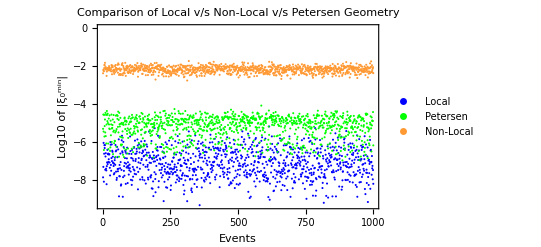

```mathematica
ListPlot[{Log10[medians[[;;,1]]],Log10[medians[[;;,3]]],Log10[medians[[;;,2]]]},PlotLegends->{Style["Local",Black,12],Style["Petersen",Black,12],Style["Non-Local",Black,12]},PlotStyle->{Blue,Green, RGBColor[255/255,153/255,51/255]},PlotLabel->Style["Comparison of Local v/s Non-Local v/s Petersen Geometry",Black,10],Frame->True,FrameLabel->{Style["Events",Black,10],Style["Log10 of |ξ_0^min|",Black,10]}]
```

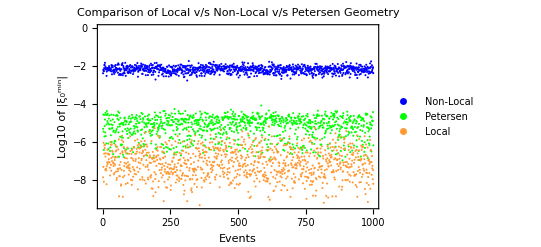

```mathematica
ListPlot[{Log10[medians[[;;,2]]],Log10[medians[[;;,3]]],Log10[medians[[;;,1]]]},PlotLegends->{Style["Non-Local",Black,12],Style["Petersen",Black,12],Style["Local",Black,12]},PlotStyle->{Blue,Green, RGBColor[255/255,153/255,51/255]},PlotLabel->Style["Comparison of Local v/s Non-Local v/s Petersen Geometry",Black,10],Frame->True,FrameLabel->{Style["Events",Black,10],Style["Log10 of |ξ_0^min|",Black,10]}]
```

# L Nl Pet Coupling

## Local

```mathematica
t=10;W=0.25;K=12; v=0.173948268172;x=0;c=1.2;
```

```mathematica
fn[t_,W_]:=RandomReal[{W-0t,W+0t},K]  (*No more a random list*)
fn2[t_,W_]:=RandomReal[{-t,t+x*t},K]  (*No more a random list*)
```

```mathematica
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
```

```mathematica
Ox = Table[0,{x,2K},{y,2K}];
```

```mathematica
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++]
i=1;While[i<K,{Ox[[i+1,i+K]] = Ox[[i+K,i+1]]=0.01^0*g2[[i]]};i++]
i=1;While[i<K,{Ox[[i,i+1+K]] = Ox[[i+K+1,i]]=0.01^0*g2[[i]]};i++]
(* No last and first site connection*)
```

```mathematica
Ox;
```

```mathematica
mat=Ox[[1;;K,K+1;;2K]]
```

(0.25 | 1.4897 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.4897 | 0.25 | 3.83113 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.83113 | 0.25 | 4.08133 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4.08133 | 0.25 | 3.63438 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3.63438 | 0.25 | -1.03399 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.03399 | 0.25 | 3.75562 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3.75562 | 0.25 | 3.61954 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3.61954 | 0.25 | -4.42977 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.42977 | 0.25 | 0.732416 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.732416 | 0.25 | -6.40268 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.40268 | 0.25 | -6.01384
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.01384 | 0.25)

```mathematica
ee=Eigenvalues[mat]
```

{9.05801,-8.55801,6.71855,6.48171,-6.21855,-5.98171,3.24485,-2.74485,2.51476,-2.01476,0.291619,0.208381}

```mathematica
ee=SingularValueDecomposition[mat][[2]]//Diagonal
```

{9.05801,8.55801,6.71855,6.48171,6.21855,5.98171,3.24485,2.74485,2.51476,2.01476,0.291619,0.208381}

```mathematica
ev=Eigenvectors[mat];
```

```mathematica
Min[Abs[ev[[-1]]]]
```

0.00352251

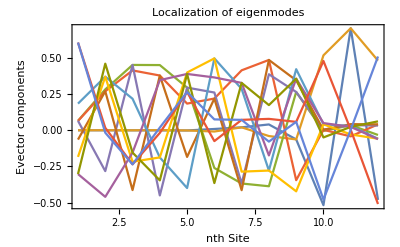

```mathematica
ListLinePlot[Table[ev[[i]],{i,1,K}],PlotRange->All,Frame->True,PlotLabel->Style["Localization of eigenmodes",Black],FrameLabel->{"nth Site","Evector components"},LabelStyle->Directive[Black],FrameTicks->{Automatic,Automatic},FrameTicksStyle->Directive[Black],AxesOrigin->{1,None},PlotRange->{{1,7},Automatic},InterpolationOrder->1]
```

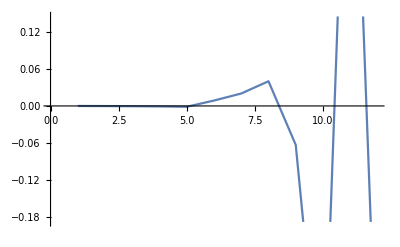

```mathematica
ListLinePlot[ev[[1]]]
```

```mathematica
{um,wm,vm}=SingularValueDecomposition[mat];
```

```mathematica
um
```

(-0.0000328728 | 0.0000328728 | -0.064928 | 0.0643528 | -0.064928 | 0.0643528 | -0.183851 | 0.183851 | -0.302254 | 0.302254 | -0.60538 | -0.60538
-0.000194364 | -0.000194364 | -0.28193 | 0.269201 | 0.28193 | -0.269201 | -0.369608 | -0.369608 | -0.459511 | -0.459511 | -0.016913 | 0.016913
-0.000434074 | 0.000434074 | -0.450769 | 0.412859 | -0.450769 | 0.412859 | -0.217439 | 0.217439 | -0.15411 | 0.15411 | 0.235213 | 0.235213
-0.000754336 | -0.000754336 | -0.449783 | 0.377689 | 0.449783 | -0.377689 | 0.187395 | 0.187395 | 0.345824 | 0.345824 | 0.0182747 | -0.0182747
-0.0013407 | 0.0013407 | -0.294331 | 0.183976 | -0.294331 | 0.183976 | 0.398599 | -0.398599 | 0.388562 | -0.388562 | -0.26393 | -0.26393
0.00876927 | 0.00876927 | 0.260361 | 0.218746 | -0.260361 | -0.218746 | -0.495827 | -0.495827 | 0.364468 | 0.364468 | 0.0748573 | -0.0748573
0.0201973 | -0.0201973 | 0.367402 | 0.413617 | 0.367402 | 0.413617 | -0.285646 | 0.285646 | 0.326764 | -0.326764 | -0.071835 | -0.071835
0.0400505 | 0.0400505 | 0.386441 | 0.485148 | -0.386441 | -0.485148 | 0.278122 | 0.278122 | -0.173714 | -0.173714 | -0.0784976 | 0.0784976
-0.063132 | 0.063132 | -0.264097 | -0.344533 | -0.264097 | -0.344533 | -0.421431 | 0.421431 | 0.35581 | -0.35581 | -0.0579586 | -0.0579586
-0.516992 | -0.516992 | 0.00480557 | 0.00281877 | -0.00480557 | -0.00281877 | -0.0411059 | -0.0411059 | 0.0495809 | 0.0495809 | -0.478059 | 0.478059
0.703992 | -0.703992 | -0.0350656 | -0.0421554 | -0.0350656 | -0.0421554 | -0.0289812 | 0.0289812 | 0.0231641 | -0.0231641 | -0.00352251 | -0.00352251
-0.480664 | -0.480664 | 0.0326007 | 0.0406816 | -0.0326007 | -0.0406816 | 0.0581961 | 0.0581961 | -0.06151 | -0.06151 | 0.508993 | -0.508993)

```mathematica
Iev=Inverse[ev];
```

```mathematica
v1=v*um[[1]];
vn=1*um[[-1]];
```

```mathematica
mm=Table[0,{i,K+1},{j,K+1}];
```

```mathematica
i=1;While[i<K+1,{mm[[i+1,i+1]]=ee[[i]]};i++]
i=1;While[i<K+1,{mm[[1,i+1]]=v1[[i]];mm[[i+1,1]]=vn[[i]]};i++]
```

```mathematica
mm
```

(0 | -5.71816×10^-6 | 5.71816×10^-6 | -0.0112941 | 0.0111941 | -0.0112941 | 0.0111941 | -0.0319805 | 0.0319805 | -0.0525766 | 0.0525766 | -0.105305 | -0.105305
-0.480664 | 9.05801 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.480664 | 0 | 8.55801 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0326007 | 0 | 0 | 6.71855 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0406816 | 0 | 0 | 0 | 6.48171 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0326007 | 0 | 0 | 0 | 0 | 6.21855 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0406816 | 0 | 0 | 0 | 0 | 0 | 5.98171 | 0 | 0 | 0 | 0 | 0 | 0
0.0581961 | 0 | 0 | 0 | 0 | 0 | 0 | 3.24485 | 0 | 0 | 0 | 0 | 0
0.0581961 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.74485 | 0 | 0 | 0 | 0
-0.06151 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.51476 | 0 | 0 | 0
-0.06151 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.01476 | 0 | 0
0.508993 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.291619 | 0
-0.508993 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.208381)

```mathematica
Eigenvalues[mm]
```

{9.05801+0. ⅈ,8.55801+0. ⅈ,6.7185+0. ⅈ,6.48178+0. ⅈ,6.21861+0. ⅈ,5.98164+0. ⅈ,3.24427+0. ⅈ,2.74553+0. ⅈ,2.51604+0. ⅈ,2.01316+0. ⅈ,0.275234+0.113072 ⅈ,0.275234-0.113072 ⅈ,-0.0502527+0. ⅈ}

```mathematica
SingularValueDecomposition[mm][[2]]//Diagonal
```

{9.07118,8.57124,6.71864,6.48185,6.21865,5.98186,3.24555,2.7457,2.51612,2.01652,0.760815,0.291613,0.0199498}

## Nonlocal

```mathematica
fn[t_,W_]:=RandomReal[{W-0t,W+0t},K]  (*No more a random list*)
fn2[t_,W_]:=RandomReal[{-t,t},K]  (*No more a random list*)
```

```mathematica
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
```

```mathematica
Ox = Table[0,{x,2K},{y,2K}];
```

```mathematica
i=1;
While[i<K+1,{j=1;
While[j<K+1,{Ox[[i,j+K]] = c*g2[[i]]/Power[c,Abs[i-j]],Ox[[j+K,i]] = c*g2[[i]]/Power[c,Abs[i-j]]};j++]};i++]
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++](*Exponentially decaying hopping terms*)
```

```mathematica
Ox
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | -8.44809 | -7.04008 | -5.86673 | -4.88894 | -4.07412 | -3.3951 | -2.82925 | -2.35771 | -1.96476 | -1.6373 | -1.36441
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.74083 | 0.25 | -4.74083 | -3.95069 | -3.29224 | -2.74354 | -2.28628 | -1.90523 | -1.58769 | -1.32308 | -1.10257 | -0.918805
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.71092 | -9.25311 | 0.25 | -9.25311 | -7.71092 | -6.42577 | -5.35481 | -4.46234 | -3.71862 | -3.09885 | -2.58237 | -2.15198
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.806612 | -0.967934 | -1.16152 | 0.25 | -1.16152 | -0.967934 | -0.806612 | -0.672177 | -0.560147 | -0.466789 | -0.388991 | -0.324159
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.21796 | -1.46155 | -1.75386 | -2.10463 | 0.25 | -2.10463 | -1.75386 | -1.46155 | -1.21796 | -1.01496 | -0.845803 | -0.704836
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.51947 | 4.22336 | 5.06804 | 6.08164 | 7.29797 | 0.25 | 7.29797 | 6.08164 | 5.06804 | 4.22336 | 3.51947 | 2.93289
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.79545 | -4.55454 | -5.46545 | -6.55853 | -7.87024 | -9.44429 | 0.25 | -9.44429 | -7.87024 | -6.55853 | -5.46545 | -4.55454
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.09274 | -3.71128 | -4.45354 | -5.34425 | -6.4131 | -7.69572 | -9.23486 | 0.25 | -9.23486 | -7.69572 | -6.4131 | -5.34425
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.93029 | -2.31635 | -2.77962 | -3.33554 | -4.00265 | -4.80318 | -5.76381 | -6.91657 | 0.25 | -6.91657 | -5.76381 | -4.80318
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.16345 | -2.59614 | -3.11537 | -3.73844 | -4.48613 | -5.38336 | -6.46003 | -7.75203 | -9.30244 | 0.25 | -9.30244 | -7.75203
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.357976 | -0.429571 | -0.515485 | -0.618582 | -0.742299 | -0.890759 | -1.06891 | -1.28269 | -1.53923 | -1.84708 | 0.25 | -1.84708
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.804253 | 0.965103 | 1.15812 | 1.38975 | 1.6677 | 2.00124 | 2.40149 | 2.88178 | 3.45814 | 4.14977 | 4.97972 | 0.25
0.25 | -4.74083 | -7.71092 | -0.806612 | -1.21796 | 3.51947 | -3.79545 | -3.09274 | -1.93029 | -2.16345 | -0.357976 | 0.804253 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.44809 | 0.25 | -9.25311 | -0.967934 | -1.46155 | 4.22336 | -4.55454 | -3.71128 | -2.31635 | -2.59614 | -0.429571 | 0.965103 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.04008 | -4.74083 | 0.25 | -1.16152 | -1.75386 | 5.06804 | -5.46545 | -4.45354 | -2.77962 | -3.11537 | -0.515485 | 1.15812 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.86673 | -3.95069 | -9.25311 | 0.25 | -2.10463 | 6.08164 | -6.55853 | -5.34425 | -3.33554 | -3.73844 | -0.618582 | 1.38975 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.88894 | -3.29224 | -7.71092 | -1.16152 | 0.25 | 7.29797 | -7.87024 | -6.4131 | -4.00265 | -4.48613 | -0.742299 | 1.6677 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.07412 | -2.74354 | -6.42577 | -0.967934 | -2.10463 | 0.25 | -9.44429 | -7.69572 | -4.80318 | -5.38336 | -0.890759 | 2.00124 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.3951 | -2.28628 | -5.35481 | -0.806612 | -1.75386 | 7.29797 | 0.25 | -9.23486 | -5.76381 | -6.46003 | -1.06891 | 2.40149 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.82925 | -1.90523 | -4.46234 | -0.672177 | -1.46155 | 6.08164 | -9.44429 | 0.25 | -6.91657 | -7.75203 | -1.28269 | 2.88178 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.35771 | -1.58769 | -3.71862 | -0.560147 | -1.21796 | 5.06804 | -7.87024 | -9.23486 | 0.25 | -9.30244 | -1.53923 | 3.45814 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.96476 | -1.32308 | -3.09885 | -0.466789 | -1.01496 | 4.22336 | -6.55853 | -7.69572 | -6.91657 | 0.25 | -1.84708 | 4.14977 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.6373 | -1.10257 | -2.58237 | -0.388991 | -0.845803 | 3.51947 | -5.46545 | -6.4131 | -5.76381 | -9.30244 | 0.25 | 4.97972 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.36441 | -0.918805 | -2.15198 | -0.324159 | -0.704836 | 2.93289 | -4.55454 | -5.34425 | -4.80318 | -7.75203 | -1.84708 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
mat=Ox[[1;;K,K+1;;2K]];
```

```mathematica
mat=(mat+Transpose[mat])/2;
```

```mathematica
ee=Eigenvalues[mat]
```

{-36.5187,10.2156,9.8541,-8.9956,8.52084,7.4661,6.75201,5.60793,-2.8312,2.02011,1.49269,-0.583886}

```mathematica
ee=SingularValueDecomposition[mat][[2]]//Diagonal
```

{36.5187,10.2156,9.8541,8.9956,8.52084,7.4661,6.75201,5.60793,2.8312,2.02011,1.49269,0.583886}

```mathematica
ev=Eigenvectors[mat];
```

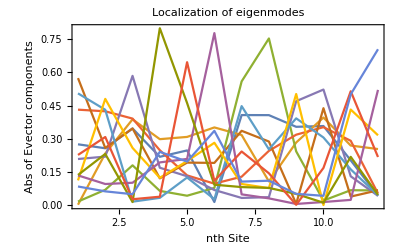

```mathematica
ListLinePlot[Abs[Table[ev[[i]],{i,1,K}]],PlotRange->All,Frame->True,PlotLabel->Style["Localization of eigenmodes",Black],FrameLabel->{"nth Site","Abs of Evector components"},LabelStyle->Directive[Black],FrameTicks->{Automatic,Automatic},FrameTicksStyle->Directive[Black],AxesOrigin->{1,None},PlotRange->{{1,7},Automatic},InterpolationOrder->1]
```

```mathematica
{um,wm,vm}=SingularValueDecomposition[mat];
```

```mathematica
um;
```

```mathematica
Iev=Inverse[ev];
```

```mathematica
v1=v*um[[1]];
vn=v*um[[-1]];
```

```mathematica
mm=Table[0,{i,K+1},{j,K+1}];
```

```mathematica
i=1;While[i<K+1,{mm[[i+1,i+1]]=ee[[i]]};i++]
i=1;While[i<K+1,{mm[[1,i+1]]=v1[[i]];mm[[i+1,1]]=vn[[i]]};i++]
```

```mathematica
mm
```

(0 | -0.0478769 | 0.000357484 | -0.00285466 | 0.0751295 | -0.0363247 | 0.0999496 | -0.0879391 | 0.0195014 | -0.0234319 | -0.0237486 | 0.0395121 | -0.0146911
-0.00732448 | 36.5187 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.044141 | 0 | 10.2156 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0115922 | 0 | 0 | 9.8541 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00914945 | 0 | 0 | 0 | 8.9956 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00736083 | 0 | 0 | 0 | 0 | 8.52084 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0116888 | 0 | 0 | 0 | 0 | 0 | 7.4661 | 0 | 0 | 0 | 0 | 0 | 0
0.00777129 | 0 | 0 | 0 | 0 | 0 | 0 | 6.75201 | 0 | 0 | 0 | 0 | 0
0.0549677 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.60793 | 0 | 0 | 0 | 0
0.0906774 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.8312 | 0 | 0 | 0
-0.00808849 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.02011 | 0 | 0
0.0378981 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.49269 | 0
-0.122642 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.583886)

```mathematica
Eigenvalues[mm]
```

{36.5187,10.2156,9.8541,8.99552,8.52081,7.46594,6.7519,5.60813,2.83045,2.02021,1.49369,0.586952,-0.00325214}

```mathematica
SingularValueDecomposition[mm][[2]]//Diagonal
```

{36.5187,10.2157,9.8541,8.99592,8.52092,7.46677,6.75258,5.60824,2.83275,2.02027,1.4937,0.596774,0.00319496}

## Petersen

```mathematica
fn[t_,W_]:=RandomReal[{W,W+0t},K]  (*No more a random list*)
fn2[t_,W_]:=RandomReal[{-t,t},2K]  (*No more a random list*)
```

```mathematica
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
```

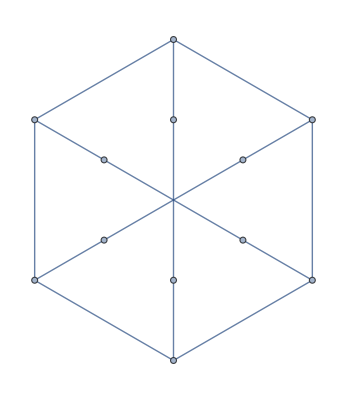

```mathematica
p =PetersenGraph[K/2,K/4,EdgeStyle->Thick]
```

```mathematica
mat = WeightedAdjacencyMatrix[p]
```

SparseArray[…]

```mathematica
i=1;
While[i<K+1,{mat[[i,i]]=g[[i]]};i++]
```

```mathematica
i=1;
While[i<K+1,{j=1;
While[j<K+1,{If[i==j,mat[[i,j]]=mat[[i,j]],mat[[i,j]]=c*g2[[i+j]]*mat[[i,j]]/Power[c,Abs[i-j]]]};j++]};i++]
```

```mathematica
mat=mat//Normal
```

(0.25 | 0 | 0 | 0.582056 | 0 | 0 | -2.84012 | 0 | 0 | 0 | 0 | 0
0 | 0.25 | 0 | 0 | -1.49841 | 0 | 0 | 1.56975 | 0 | 0 | 0 | 0
0 | 0 | 0.25 | 0 | 0 | 4.34172 | 0 | 0 | -2.35646 | 0 | 0 | 0
0.582056 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | -1.62891 | 0 | 0
0 | -1.49841 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | -3.17354 | 0
0 | 0 | 4.34172 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | 2.03595
-2.84012 | 0 | 0 | 0 | 0 | 0 | 0.25 | 2.98413 | 0 | 0 | 0 | 4.16619
0 | 1.56975 | 0 | 0 | 0 | 0 | 2.98413 | 0.25 | 8.24642 | 0 | 0 | 0
0 | 0 | -2.35646 | 0 | 0 | 0 | 0 | 8.24642 | 0.25 | 8.63901 | 0 | 0
0 | 0 | 0 | -1.62891 | 0 | 0 | 0 | 0 | 8.63901 | 0.25 | 4.73287 | 0
0 | 0 | 0 | 0 | -3.17354 | 0 | 0 | 0 | 0 | 4.73287 | 0.25 | -3.47027
0 | 0 | 0 | 0 | 0 | 2.03595 | 4.16619 | 0 | 0 | 0 | -3.47027 | 0.25)

```mathematica
ee=SingularValueDecomposition[mat][[2]]//Diagonal
```

{13.2346,12.7346,7.70187,7.20187,4.8649,4.3649,3.17523,2.67523,2.18475,1.68475,0.28156,0.21844}

```mathematica
ev=Eigenvectors[mat];
```

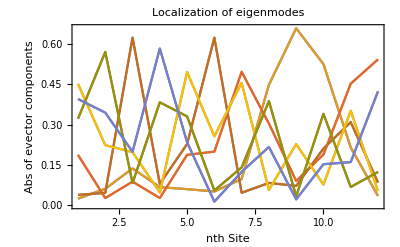

```mathematica
ListLinePlot[Abs[Table[ev[[i]],{i,1,K}]],PlotRange->All,Frame->True,PlotLabel->Style["Localization of eigenmodes",Black],FrameLabel->{"nth Site","Abs of evector components"},LabelStyle->Directive[Black],FrameTicks->{Automatic,Automatic},FrameTicksStyle->Directive[Black],AxesOrigin->{1,None},PlotRange->{{1,7},Automatic}]
```

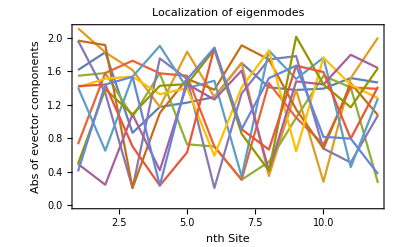

```mathematica
ListLinePlot[Abs[Table[Abs[Log10[ev[[i]]]],{i,1,K}]],PlotRange->All,Frame->True,PlotLabel->Style["Localization of eigenmodes",Black],FrameLabel->{"nth Site","Abs of evector components"},LabelStyle->Directive[Black],FrameTicks->{Automatic,Automatic},FrameTicksStyle->Directive[Black],AxesOrigin->{1,None},PlotRange->{{1,7},Automatic}]
```

```mathematica
{um,wm,vm}=SingularValueDecomposition[mat];
```

```mathematica
um;
```

```mathematica
Iev=Inverse[ev];
```

```mathematica
v1=v*um[[1]];
vn=1*um[[-1]];
```

```mathematica
mm=Table[0,{i,K+1},{j,K+1}];
```

```mathematica
i=1;While[i<K+1,{mm[[i+1,i+1]]=ee[[i]]};i++]
i=1;While[i<K+1,{mm[[1,i+1]]=v1[[i]];mm[[i+1,1]]=vn[[i]]};i++]
```

```mathematica
mm;
```

```mathematica
ev1=SingularValueDecomposition[mm][[2]]//Diagonal
```

{13.2346,12.7346,7.72193,7.22169,4.86563,4.36572,3.17665,2.67692,2.18919,1.69067,0.646621,0.250665,0.0830512}

```mathematica
svd=SingularValueDecomposition[mm];
```

```mathematica
svd[[1]]
```

(0.00131105 | -0.0000352291 | 0.000289849 | -0.00835841 | -0.00426404 | -0.0133929 | 0.0130085 | 0.00347489 | 0.00825797 | -0.0117646 | 0.0264504 | 0.0239371 | 0.999035
-0.999999 | 2.12988×10^-7 | 4.78508×10^-7 | -0.0000116124 | -5.86937×10^-6 | -0.0000182575 | 0.000017614 | 4.97516×10^-6 | 0.0000103899 | -0.0000155159 | 0.0000349452 | 0.0000320626 | 0.00130974
-2.59122×10^-7 | -1. | 0.0000703826 | 0.0000185536 | 0.0000107259 | 0.000011625 | -6.63581×10^-6 | 0.0000331354 | -0.0000419436 | -3.15745×10^-6 | 0.0000155513 | 0.0000510898 | -0.0000362815
-9.84935×10^-8 | -0.0000703913 | -1. | -7.97229×10^-6 | -1.41225×10^-6 | -5.83301×10^-6 | 5.35866×10^-6 | 0.0000112034 | -9.21566×10^-6 | -4.57284×10^-6 | 0.0000125065 | 0.0000216205 | 0.00028904
6.5382×10^-7 | -0.000018251 | 5.55065×10^-6 | -0.999965 | 0.00035469 | 0.000363889 | -0.000250897 | -0.0000372982 | -0.0000879646 | 0.000102505 | -0.000222734 | -0.000186906 | -0.0083441
-2.79043×10^-7 | 0.0000105782 | -1.7885×10^-7 | 0.000318977 | 0.999991 | -0.000251092 | 0.000151197 | 0.0000162948 | 0.000049934 | -0.0000522653 | 0.000112342 | 0.0000900819 | 0.00425924
6.98608×10^-7 | -0.0000111565 | 1.95331×10^-6 | -0.000251921 | -0.000193793 | -0.99991 | -0.000965777 | -0.0000802793 | -0.000151397 | 0.000168094 | -0.000360522 | -0.000296687 | -0.0133749
-5.60186×10^-7 | 6.19451×10^-6 | -1.59205×10^-6 | 0.00014246 | 0.0000958326 | 0.000791402 | -0.999915 | 0.000115703 | 0.000149324 | -0.000166766 | 0.00035538 | 0.000293194 | 0.0130121
4.19299×10^-7 | 0.0000332352 | 0.0000101885 | -8.30119×10^-6 | -1.49692×10^-6 | -0.0000338201 | 0.0000704127 | 0.999994 | 0.000174647 | 0.0000633743 | -0.000170812 | -0.000300501 | -0.00346865
4.35426×10^-7 | 0.0000415817 | 0.0000115837 | 0.0000189943 | 0.0000147161 | 0.000040823 | -0.0000416804 | 0.000203025 | -0.999965 | -0.0000106225 | -0.000294977 | -0.00124118 | 0.00830368
-9.18686×10^-8 | -3.54464×10^-6 | -1.15749×10^-6 | 4.25428×10^-6 | 2.1162×10^-6 | 0.0000106044 | -0.0000135208 | -0.0000223483 | 0.0000858871 | 0.999931 | 0.000852927 | 0.000574017 | 0.0117386
2.66574×10^-7 | 0.0000163641 | 4.81088×10^-6 | -1.85411×10^-6 | 3.91415×10^-7 | -6.47868×10^-6 | 0.0000109118 | 0.0000783584 | -0.000510008 | -0.000540959 | 0.999646 | -0.00323125 | -0.0263919
-6.82194×10^-7 | -0.0000520569 | -0.0000147189 | -0.0000130472 | -0.0000119894 | -0.0000238063 | 0.0000185567 | -0.000217834 | 0.00144098 | 0.00029407 | -0.00259655 | -0.999707 | 0.0240135)